This document is long enough that it is annoying to have all the sections open at once.

CDF users: look through the menu items to find out how to expand sections. Alternatively, the shortcut should be Ctrl+‘
Mathematica users: I recommend enabling “Preferences>Interface>Show open/close icon for cell groups” to help with section management.

### Init

Macro to help with exporting figures.

```mathematica
$doExport=False;
exportme[name_,opt:OptionsPattern[Export]][fig_]:=(SetDirectory[NotebookDirectory[]];
If[$doExport,
Export["../fig/"<>name<>".pdf",fig,opt];Export["../fig/"<>name<>".png",fig,opt]];fig)
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

Symbolic assumptions used globally:

```mathematica
$Assumptions=0<β<γ<α&&0≤p≤1&&x>=0&&y>=0&&z>=0&&λ∈Reals&&x∈Integers&&y∈Integers&&z∈Integers&&k≥0&&k∈Integers&&-1<t<0;
```

### Log-Likelihood Function

```mathematica
L=(α^x Exp[-α])/Factorial[x]*(β^y Exp[-β])/Factorial[y]*((p α+(1-p)β)^z Exp[-(p α+(1-p)β)])/Factorial[z];
LL=Log[L]//FullSimplify
```

-(1+p) α+(-2+p) β+Log[(α^x β^y (p (α-β)+β)^z)/(x! y! z!)]

### Data Creation

It will be useful to have a function that samples random data from our prior.

```mathematica
betaDistribution[μ_,σ_]:=BetaDistribution[(μ^2-μ^3-μ σ^2)/σ^2,((-1+μ) (-μ+μ^2+σ^2))/σ^2];
gammaDistribution[μ_,σ_]:=GammaDistribution[μ^2/σ^2,σ^2/μ];
MonteCarloData[nshots_,nsamples_]:=Module[{p,Γ,α,β,κ,μ,n=nshots,data,samples=nsamples,Ls},
Γ=RandomVariate[gammaDistribution[n*0.003,n*0.001],samples];
μ=RandomVariate[gammaDistribution[n*0.007,n*0.001],samples];
κ=RandomVariate[betaDistribution[0.65,0.05],samples];
α=Γ+μ;
β=Γ+κ*μ;
p=RandomVariate[UniformDistribution[],samples];
data={N@RandomVariate[PoissonDistribution[#]]&/@α,
N@RandomVariate[PoissonDistribution[#]]&/@β,
N@RandomVariate[PoissonDistribution[#]]&/@(p α+(1-p)β)}ᵀ
]
```

### Lagrange Multipliers

```mathematica
$Assumptions=0<β<γ<α&&0≤p≤1&&x>0&&y>0&&z>0&&λ∈Reals;
```

We want to maximize the likelihood for all three of α, β, p in this case. We can set this up as a lagrange multiplier problem.

```mathematica
Φ=Log[α^x Exp[-α]/Factorial[x]*β^y Exp[-β]/Factorial[y]*(p α+(1-p)β)^z Exp[-γ]/Factorial[z]]-λ (γ-(p α+(1-p)β));
```

Get a system of equations from this, and eliminate γ and λ

```mathematica
lagrangeEquations=D[Φ,#]==0&/@{α,β,γ,λ,p}//FullSimplify
lagrangeEquations=Rest[lagrangeEquations]/.First@Solve[First@lagrangeEquations,λ]//FullSimplify
lagrangeEquations=lagrangeEquations[[{1,2,4}]]/.First@Solve[lagrangeEquations[[3]],γ]
```

{(x-α) β+p^2 α (α-β) λ+p (x (α-β)+α (z-α+β+β λ))==0,β (y+z+β (-1+λ))+p^2 β (-α+β) λ+p (y (α-β)-β (z+α-β-α λ+2 β λ))==0,1+λ==0,p α+β==p β+γ,z+(p α+β) λ==p β λ}

{(p y α+((-1+p) x+α-2 p α) β)/p==0,α (-x-z+α+p α)==((-1+p) (-x+α+p α) β)/p,p α+β==p β+γ,(x-α)/p==0}

{(p y α+((-1+p) x+α-2 p α) β)/p==0,α (-x-z+α+p α)==((-1+p) (-x+α+p α) β)/p,(x-α)/p==0}

```mathematica
soln=Solve[lagrangeEquations,{α,β,p}]//FullSimplify
```

{{α→x,β→y,p→(-y+z)/(x-y)}}

### Profiled Likelihood

Messing around with profiled likelihood functions; no good came of it.

#### p first

```mathematica
psol=First@Solve[D[L,p]==0//FullSimplify,p]//FullSimplify
```

{p→(z-β)/(α-β)}

```mathematica
D[D[L,p],p]/.psol//FullSimplify
```

-(α-β)^2/z

```mathematica
L/.psol
```

-α (1+(z-β)/(α-β))+(-2+(z-β)/(α-β)) β+Log[(z^z α^x β^y)/(x! y! z!)]

```mathematica
αsol=First@Solve[D[L/.psol,α]==0//FullSimplify,α]//FullSimplify
```

{α→x}

```mathematica
Solve[D[L/.psol,β]==0//FullSimplify,β]//FullSimplify
```

{{β→y}}

#### α, β first

There are two critical points when we look at just alpha. Which one to choose?

```mathematica
αsol=Solve[D[L,α]==0//FullSimplify,α]//FullSimplify
```

{{α→-(-p (x+z)+β-p^2 β+√(-4 p (-1+p^2) x β+(β-p (x+z+p β))^2))/(2 p (1+p))},{α→(p (x+z)-β+p^2 β+√(-4 p (-1+p^2) x β+(β-p (x+z+p β))^2))/(2 p (1+p))}}

Only the second results in positive values of α.

```mathematica
Reduce[(α/.First@αsol)>0]//FullSimplify
Reduce[(α/.Last@αsol)>0]//FullSimplify
```

False

p>0

And if we look at the second derivatives it is a maximum:

```mathematica
Reduce[((D[D[L,α],α]//FullSimplify)/.Last@αsol)<0]//FullSimplify
```

p>0

Next try to maximize β in the likilihood replaced with our max forα:

```mathematica
βsol=Solve[D[L/.Last@αsol,β]==0//FullSimplify,β]//FullSimplify
```

{{β→(p (x-z+2 ⅈ √(x z)))/(-1+p^2)},{β→(p (x-z-2 ⅈ √(x z)))/(-1+p^2)},{β→(y+p^2 (x+y)+z-2 p (x+2 y+z)+√(4 (-2+p) p (-1+2 p) y (x+y+z)+(y+p^2 (x+y)+z-2 p (x+2 y+z))^2))/(2 (-2+p) (-1+2 p))},{β→(y+p^2 (x+y)+z-2 p (x+2 y+z)-√(4 (-2+p) p (-1+2 p) y (x+y+z)+(y+p^2 (x+y)+z-2 p (x+2 y+z))^2))/(2 (-2+p) (-1+2 p))}}

Check which one is positive:

```mathematica
Reduce[(β/.βsol[[3]])>=0]//FullSimplify
Reduce[(β/.βsol[[4]])>=0]//FullSimplify
```

2 p≠1

p≤0||2 p>1

The following takes to long to evaluate, lets just assume the first one

```mathematica
Reduce[((D[D[(L/.Last@αsol)//Simplify,β]//Simplify,β]//FullSimplify)/.βsol[[3]])<0]//FullSimplify
Reduce[((D[D[(L/.Last@αsol)//Simplify,β]//Simplify,β]//FullSimplify)/.βsol[[4]])<0]//FullSimplify
```

$Aborted

$Aborted

```mathematica
Join[Last@αsol/.βsol[[3]],βsol[[3]]]//Simplify
```

{α→1/(2 p (1+p))(p (x+z)-(y+p^2 (x+y)+z-2 p (x+2 y+z)+√(4 (-2+p) p (-1+2 p) y (x+y+z)+(y+p^2 (x+y)+z-2 p (x+2 y+z))^2))/(2 (-2+p) (-1+2 p))+(p^2 (y+p^2 (x+y)+z-2 p (x+2 y+z)+√(4 (-2+p) p (-1+2 p) y (x+y+z)+(y+p^2 (x+y)+z-2 p (x+2 y+z))^2)))/(2 (-2+p) (-1+2 p))+√(-(2 p (-1+p^2) x (y+p^2 (x+y)+z-2 p (x+2 y+z)+√(4 (-2+p) p (-1+2 p) y (x+y+z)+(y+p^2 (x+y)+z-2 p (x+2 y+z))^2)))/((-2+p) (-1+2 p))+(-(y+p^2 (x+y)+z-2 p (x+2 y+z)+√(4 (-2+p) p (-1+2 p) y (x+y+z)+(y+p^2 (x+y)+z-2 p (x+2 y+z))^2))/(2 (-2+p) (-1+2 p))+p (x+z+(p (y+p^2 (x+y)+z-2 p (x+2 y+z)+√(4 (-2+p) p (-1+2 p) y (x+y+z)+(y+p^2 (x+y)+z-2 p (x+2 y+z))^2)))/(2 (-2+p) (-1+2 p))))^2)),β→(y+p^2 (x+y)+z-2 p (x+2 y+z)+√(4 (-2+p) p (-1+2 p) y (x+y+z)+(y+p^2 (x+y)+z-2 p (x+2 y+z))^2))/(2 (-2+p) (-1+2 p))}

```mathematica
βsol[[3]]
```

{β→(y+p^2 (x+y)+z-2 p (x+2 y+z)+√(4 (-2+p) p (-1+2 p) y (x+y+z)+(y+p^2 (x+y)+z-2 p (x+2 y+z))^2))/(2 (-2+p) (-1+2 p))}

```mathematica
Solve[D[L/.Join[Last@αsol,βsol[[3]]],p]==0//FullSimplify,p]
```

$Aborted

### Integrated Likelihood

Messing around with integrated likelihood function; no good came of it.

```mathematica
Integrate[(α^x Exp[-α])/Factorial[x]*(β^y Exp[-β])/Factorial[y]*((p α+(1-p)β)^z Exp[-(p α+(1-p)β)])/Factorial[z],{α,0,c}]
```

∫_0^c (ⅇ^(-α-p α-β-(1-p) β) α^x β^y (p α+(1-p) β)^z)/(x! y! z!)ⅆα

```mathematica
Integrate[Sqrt[x^2+1],{x,1,c}]//FullSimplify
```

ConditionalExpression[1/2 (-√2+c √(1+c^2)-ArcSinh[1]+ArcSinh[c]),Re[c]>1&&Im[c]==0]

```mathematica
ConditionalExpression[1/2 (-√2+c √(1+c^2)-ArcSinh[1]+ArcSinh[c]),Re[c]>1&&Im[c]==0]//FullSimplify
```

ConditionalExpression[1/2 (-√2+c √(1+c^2)-ArcSinh[1]+ArcSinh[c]),Re[c]>1&&Im[c]==0]

```mathematica
Plot[ArcSinh[c]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[ArcSinh[c]]

```mathematica
Limit[Sqrt[n^2+1]-n+2,n->∞]
```

2

```mathematica
QUDoc@FindPulse
```

### Profiled Bayes estimate

Messing around with profiled Bayes’ estimates; no good game of it.

```mathematica
Lp[p_,z_,α_,β_]=((p α+(1-p)β)^z Exp[-(p α+(1-p)β)])/Factorial[z];
```

```mathematica
prior[p_]:=1
```

```mathematica
denom=Integrate[Lp[p,z,α,β]prior[p],{p,0,1}]//FullSimplify
```

(-Gamma[1+z,α]+Gamma[1+z,β])/((α-β) z!)

```mathematica
posterior[p_,z_,α_,β_]=Lp[p,z,α,β]prior[p]/denom
```

(ⅇ^(-p α-(1-p) β) (α-β) (p α+(1-p) β)^z)/(-Gamma[1+z,α]+Gamma[1+z,β])

```mathematica
estBayes=Integrate[p*posterior[p,z,α,β],{p,0,1}]//FullSimplify
```

(-β Gamma[1+z,α]+β Gamma[1+z,β]+Gamma[2+z,α]-Gamma[2+z,β])/((α-β) (Gamma[1+z,α]-Gamma[1+z,β]))

```mathematica
(estBayes-p)/.{α->α*nshots,β->β*nshots}
```

-p+(-nshots β Gamma[1+z,nshots α]+nshots β Gamma[1+z,nshots β]+Gamma[2+z,nshots α]-Gamma[2+z,nshots β])/((nshots α-nshots β) (Gamma[1+z,nshots α]-Gamma[1+z,nshots β]))

### Fisher Information

Quick check that sums are working over the likelihood:

```mathematica
Sum[L,{x,0,∞},{y,0,∞},{z,0,∞}]//Simplify
```

1

Now get Fisher matrix:

```mathematica
Ifisher=-Sum[Evaluate[Simplify[Outer[D[LL,#1,#2]&,{p,α,β},{p,α,β}]L]],{x,0,∞},{y,0,∞},{z,0,∞}]//FullSimplify;
Ifisher//MatrixForm
```

((α-β)^2/(p (α-β)+β) | (p (α-β))/(p (α-β)+β) | -1+α/(p α+β-p β)
(p (α-β))/(p (α-β)+β) | 1/α+p^2/(p α+β-p β) | -((-1+p) p)/(p (α-β)+β)
-1+α/(p α+β-p β) | -((-1+p) p)/(p (α-β)+β) | (p α+(-2+p) (-1+p) β)/(β (p (α-β)+β)))

```mathematica
Iinv=Ifisher//Inverse//FullSimplify;
Iinv//MatrixForm
```

((p (1+p) α+(-2+p) (-1+p) β)/(α-β)^2 | (p α)/(-α+β) | ((-1+p) β)/(α-β)
(p α)/(-α+β) | α | 0
((-1+p) β)/(α-β) | 0 | β)

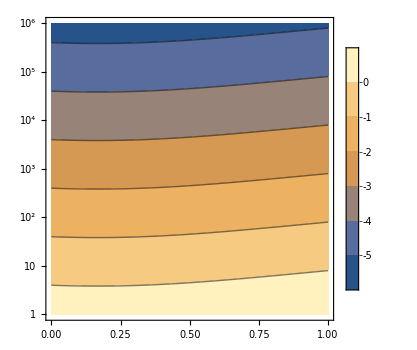

```mathematica
exportme["cramer-rao"]@ContourPlot[
Log10@Iinv[[1,1]]//.{β->1/2 α,α->10^n},{p,0,1},{n,0,6},
FrameTicks->{{Table[{n,("10")^n},{n,0,6}],None},{Automatic,Automatic}},
FrameLabel->MaTeX[{"p","\\alpha"},FontSize->14],
ImageSize->350,
PlotLabel->MaTeX["\\text{Cram\\'er-Rao bound of }\\log_{10}\\text{Var}[p]",FontSize->14],
PlotLegends->BarLegend[Automatic,Table[{n,0},{n,0,-4}],LabelStyle->texStyle,LegendMargins->0,LegendMarkerSize->300,LegendLabel->None],
BaseStyle->texStyle
]
```

Find the high order gradients too:

```mathematica
K=With[{summand=FullSimplify[L*Outer[D[LL,#1,#2,#3]&,{p,α,β},{p,α,β},{p,α,β}]]},Sum[summand,{x,0,∞},{y,0,∞},{z,0,∞}]]//FullSimplify;
MatrixForm/@K
```

{((2 (α-β)^3)/(p (α-β)+β)^2 | (2 β (-α+β))/(p (α-β)+β)^2 | (2 α (α-β))/(p (α-β)+β)^2
(2 β (-α+β))/(p (α-β)+β)^2 | -(2 p β)/(p (α-β)+β)^2 | (-β+p (α+β))/(p (α-β)+β)^2
(2 α (α-β))/(p (α-β)+β)^2 | (-β+p (α+β))/(p (α-β)+β)^2 | -(2 (-1+p) α)/(p (α-β)+β)^2),((2 β (-α+β))/(p (α-β)+β)^2 | -(2 p β)/(p (α-β)+β)^2 | (-β+p (α+β))/(p (α-β)+β)^2
-(2 p β)/(p (α-β)+β)^2 | 2 (1/α^2+p^3/(p (α-β)+β)^2) | -(2 (-1+p) p^2)/(p (α-β)+β)^2
(-β+p (α+β))/(p (α-β)+β)^2 | -(2 (-1+p) p^2)/(p (α-β)+β)^2 | (2 (-1+p)^2 p)/(p (α-β)+β)^2),((2 α (α-β))/(p (α-β)+β)^2 | (-β+p (α+β))/(p (α-β)+β)^2 | -(2 (-1+p) α)/(p (α-β)+β)^2
(-β+p (α+β))/(p (α-β)+β)^2 | -(2 (-1+p) p^2)/(p (α-β)+β)^2 | (2 (-1+p)^2 p)/(p (α-β)+β)^2
-(2 (-1+p) α)/(p (α-β)+β)^2 | (2 (-1+p)^2 p)/(p (α-β)+β)^2 | 2/β^2-(2 (-1+p)^3)/(p (α-β)+β)^2)}

```mathematica
J=With[{summand=L*FullSimplify[Outer[D[LL,#2,#3]*D[LL,#1]&,{p,α,β},{p,α,β},{p,α,β}]]},Sum[summand,{x,0,∞},{y,0,∞},{z,0,∞}]]//FullSimplify;
MatrixForm/@J
```

```mathematica
{({{(-α+β)^3/(p (α-β)+β)^2, ((α-β) β)/(p (α-β)+β)^2, (α (-α+β))/(p (α-β)+β)^2}, {((α-β) β)/(p (α-β)+β)^2, (p^2 (-α+β))/(p (α-β)+β)^2, ((-1+p) p (α-β))/(p (α-β)+β)^2}, {(α (-α+β))/(p (α-β)+β)^2, ((-1+p) p (α-β))/(p (α-β)+β)^2, -((-1+p)^2 (α-β))/(p (α-β)+β)^2}}),({{-(p (α-β)^2)/(p (α-β)+β)^2, (p β)/(p (α-β)+β)^2, -(p α)/(p (α-β)+β)^2}, {(p β)/(p (α-β)+β)^2, -1/α^2-p^3/(p (α-β)+β)^2, ((-1+p) p^2)/(p (α-β)+β)^2}, {-(p α)/(p (α-β)+β)^2, ((-1+p) p^2)/(p (α-β)+β)^2, -((-1+p)^2 p)/(p (α-β)+β)^2}}),({{((-1+p) (α-β)^2)/(p (α-β)+β)^2, -((-1+p) β)/(p (α-β)+β)^2, ((-1+p) α)/(p (α-β)+β)^2}, {-((-1+p) β)/(p (α-β)+β)^2, ((-1+p) p^2)/(p (α-β)+β)^2, -((-1+p)^2 p)/(p (α-β)+β)^2}, {((-1+p) α)/(p (α-β)+β)^2, -((-1+p)^2 p)/(p (α-β)+β)^2, -1/β^2+(-1+p)^3/(p (α-β)+β)^2}})}
```

```mathematica
bias=Table[Sum[Iinv[[s,i]]*Iinv[[j,k]](K[[i,j,k]]/2+J[[i,j,k]]),{i,3},{j,3},{k,3}],{s,3}]//FullSimplify
```

{0,α/(-α+β),β/(α-β)}

### Biased Cramer-Rao

The MLE has the following bias +O((α+β)^-2):

```mathematica
abias=(p-β/(α+β))(α+β)/(α-β)^2;
```

Then this is approximately the expected value of the MLE:

```mathematica
aexpect=abias+p;
```

We get the Jacobian of the expected value of the full estimator of (p,α,β) as:

```mathematica
(MLEJac=D[{aexpect,α,β},{{p,α,β}}]//FullSimplify)//MatrixForm
```

(1+(α+β)/(α-β)^2 | (2 β-p (α+3 β))/(α-β)^3 | ((-1+3 p) α+(-1+p) β)/(α-β)^3
0 | 1 | 0
0 | 0 | 1)

```mathematica
(CRBBiased=MLEJac.Iinv.MLEJacᵀ//FullSimplify)//MatrixForm
```

((p α^3 ((1+α)^2+p (2+α)^2)+α^2 (5+2 α (3+α)+p^2 (32+(8-3 α) α)-p (23+α (20+7 α))) β+α (14-41 p+32 p^2-6 (1-2 p)^2 α+2 (-4+p (9+p)) α^2) β^2+(5+p (-9+4 p)-6 α+4 p (1+2 p) α+2 (6+(-11+p) p) α^2) β^3+(6-8 α+p (-10+p (4-3 α)+13 α)) β^4+(-2+p) (-1+p) β^5)/(α-β)^6 | (α (2 β-p (α^2-2 α (-1+β)+β (4+β))))/(α-β)^3 | (β ((-1+p) α^2+(-1+p) β (2+β)+2 α (-1-p (-2+β)+β)))/(α-β)^3
(α (2 β-p (α^2-2 α (-1+β)+β (4+β))))/(α-β)^3 | α | 0
(β ((-1+p) α^2+(-1+p) β (2+β)+2 α (-1-p (-2+β)+β)))/(α-β)^3 | 0 | β)

Consider a change of variables to contrast and scale:

```mathematica
reps=First@Solve[{c==(α-β)/(α+β),s==1/(α+β)},{α,β}]
```

{α→-(-1-c)/(2 s),β→-(-1+c)/(2 s)}

And truncate expression to 1st order in scale, since our expression for bias was only good to first order in scale. We get the Fisher Info back exactly; the bias is too small to matter.

```mathematica
Normal@Series[CRBBiased[[1,1]]/.reps//FullSimplify,{s,0,1}]/.{c->(α-β)/(α+β),s->1/(α+β)}//FullSimplify
```

(p (1+p) α+(-2+p) (-1+p) β)/(α-β)^2

We can plot both bounds. However, this is not useful because we have not included higher order corrections to the bias.

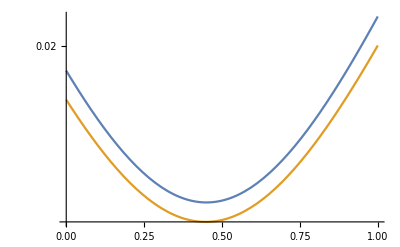

```mathematica
With[{expr={CRBBiased[[1,1]],Iinv[[1,1]]}/.{α->10000,β->9000}},LogPlot[expr,{p,0,1}]]
```

### MLE Bias ϵ

```mathematica
$Assumptions=0<β<γ<α&&0≤p≤1&&x>=0&&y>=0&&z>=0&&λ∈Reals&&x∈Integers&&y∈Integers&&z∈Integers&&ϵ>0;
```

```mathematica
L
```

(ⅇ^(-α-p α-β-(1-p) β) α^x β^y (p α+(1-p) β)^z)/(x! y! z!)

Likelihood with variable change γ=pα+(1-p)β

```mathematica
Lo=(ⅇ^(-α-γ-β) α^x β^y γ^z)/(x! y! z!);
```

We have three variables to sum over to get the expectation value. Sum over z first, easy enough:

```mathematica
Sum[(z-y)/(x-y+ϵ)Lo,{z,0,∞}]//FullSimplify
```

-(ⅇ^(-α-β) α^x β^y (y-γ))/((x-y+ϵ) x! y!)

Then over x. Not so easy, but it still does something:

```mathematica
Sum[-(ⅇ^(-α-β) α^x β^y (y-γ))/((x-y+ϵ) x! y!),{x,0,∞}]//FullSimplify
```

(ⅇ^(-α-β) (-α)^(y-ϵ) β^y (-y+γ) (Gamma[-y+ϵ]-Gamma[-y+ϵ,-α]))/(y!)

When we try to sum the result over y, it fails to compute. Let’s expand it a bit, and look at the terms one at a time:

```mathematica
(ⅇ^(-α-β) (-α)^(y-ϵ) β^y (-y+γ) (Gamma[-y+ϵ]-Gamma[-y+ϵ,-α]))/(y!)//FunctionExpand
```

-(ⅇ^(-α-β) (-α)^(y-ϵ) β^y Gamma[-y+ϵ])/Gamma[y]+(ⅇ^(-α-β) (-α)^(y-ϵ) β^y γ Gamma[-y+ϵ])/Gamma[1+y]+(ⅇ^(-α-β) (-α)^(y-ϵ) β^y Gamma[-y+ϵ,-α])/Gamma[y]-(ⅇ^(-α-β) (-α)^(y-ϵ) β^y γ Gamma[-y+ϵ,-α])/Gamma[1+y]

The first two terms are purely imaginary, and therefore can be ignored since we know the final result is real; the imaginary part must be cancelled out in the last two terms. Sum over y on the last two terms:

```mathematica
Sum[-(ⅇ^(-α-β) (-α)^(y-ϵ) β^y Gamma[-y+ϵ])/Gamma[y],{y,0,∞}]
Sum[(ⅇ^(-α-β) (-α)^(y-ϵ) β^y γ Gamma[-y+ϵ])/Gamma[1+y],{y,0,∞}]
```

ⅇ^(-α-β) (-α)^-ϵ √α (√α √β)^ϵ √β BesselI[1-ϵ,2 √α √β] Gamma[2-ϵ] Gamma[-1+ϵ]

ⅇ^(-α-β) (-α)^-ϵ (α β)^(ϵ/2) γ BesselI[-ϵ,2 √(α β)] Gamma[1-ϵ] Gamma[ϵ]

The second two terms look good as we plot against y with some α,β,γ.

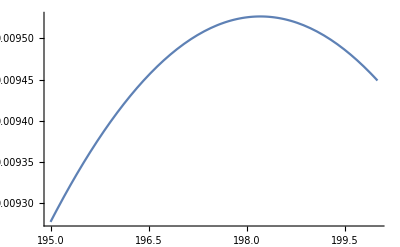

```mathematica
Plot[Re[(ⅇ^(-α-β) (-α)^(y-ϵ) β^y Gamma[-y+ϵ,-α])/Gamma[y]-(ⅇ^(-α-β) (-α)^(y-ϵ) β^y γ Gamma[-y+ϵ,-α])/Gamma[1+y]/.{ϵ->0.1,α->500.,β->200,γ->300}],{y,195,200}]
```

Now we use the formula Γ(s,x)=(∫_x)^∞t^(s-1)e^-t dt, switch the order of the sum with the integral, make the change of variables t->α,t, and we can do the sum:

```mathematica
Sum[-γ Exp[-α-β] β^y(-1)^(y-ϵ)(t)^(-y+ϵ-1)Exp[-α t]/Factorial[y],{y,0,∞}]//FullSimplify
Sum[ Exp[-α-β] β^y(-1)^(y-ϵ)( t)^(-y+ϵ-1)Exp[-α t]/Gamma[y],{y,0,∞}]//FullSimplify
```

(-1)^(1-ϵ) ⅇ^(-((1+t) (t α+β))/t) t^(-1+ϵ) γ

(-1)^(1-ϵ) ⅇ^(-((1+t) (t α+β))/t) t^(-2+ϵ) β

We are interested in (the real part of) the sum:

```mathematica
(-1)^(1-ϵ) ⅇ^(-((1+t) (t α+β))/t) t^(-2+ϵ) β+(-1)^(1-ϵ) ⅇ^(-((1+t) (t α+β))/t) t^(-1+ϵ) γ//FullSimplify
```

(-1)^(1-ϵ) ⅇ^(-((1+t) (t α+β))/t) t^(-2+ϵ) (β+t γ)

Perform the following change of variables

```mathematica
t=Exp[I ϕ]
dt=I Exp[I ϕ]dϕ=I t dϕ
```

to get

```mathematica
expr=((-1)^(1-ϵ) ⅇ^(-((1+t) (t α+β))/t) t^(-2+ϵ) (β+t γ)I t)/.{t->Exp[I ϕ]}//FullSimplify
```

ⅈ (-1)^(1-ϵ) ⅇ^(-ⅇ^(-ⅈ ϕ) (1+ⅇ^(ⅈ ϕ)) (ⅇ^(ⅈ ϕ) α+β)) (ⅇ^(ⅈ ϕ))^(-1+ϵ) (β+ⅇ^(ⅈ ϕ) γ)

Closer look at the exponent

```mathematica
-((1+t) (t α+β))/t//Expand
```

-α-t α-β-β/t

Monte carlo-estimator for the bias to compare with:

```mathematica
Module[{α=500,β=300,p=.75,n=10000000,x,y,z},
x=N@RandomVariate[PoissonDistribution[α],n];
y=RandomVariate[PoissonDistribution[β],n];
z=RandomVariate[PoissonDistribution[p α+(1-p)β],n];
(z-y)/(x-y+.2)
]//Mean
```

0.757144

Try out a few different expressions

```mathematica
NIntegrate[I(-1)^-ϵ ⅇ^(-α(1+Exp[I ϕ])-β(1+Exp[-I ϕ]))(γ Exp[I ϵ ϕ]+β Exp[I (ϵ-1)ϕ])/.{ϵ->.2,α->500,β->300.,γ->450},{ϕ,0,π}]
NIntegrate[expr/.{ϵ->.2,α->500,β->300.,γ->450},{ϕ,π,0}]
NIntegrate[(-1)^(1-ϵ) ⅇ^(-((1+t) (t α+β))/t) t^(-2+ϵ) (β+t γ)/.{ϵ->0,α->500,β->300.,γ->450},{t,-1,I}]
NIntegrate[Exp[-(α+β)(1+Cos[ϕ])]((γ+β Cos[ϕ])Sin[(α-β)Sin[ϕ]]+β Sin[ϕ]Cos[(α-β)Sin[ϕ]])/.{ϵ->.2,α->500,β->300.,γ->450},{ϕ,0,π}]
```

0.757156+2.49371×10^-11 ⅈ

0.757156

0.757938+2.62271×10^-11 ⅈ

0.757938

```mathematica
Table[{Abs[bias[1,10^n,0.5 10^n]-bias2[1,10^n,0.5 10^n]],(1/10^n)},{n,0,5}]ᵀ
```

{{0.431018,0.726693,0.192948,8.46424×10^-6,8.03377×10^-8,8.00751×10^-10},{1,1/10,1/100,1/1000,1/10000,1/100000}}

```mathematica
Table[{bias[1,10^n,0.5 10^n],bias3[1,10^n,0.5 10^n],(1/10^n)},{n,0,5}]ᵀ
```

{{-0.992545,-0.734906,-0.141501,0.00406579,0.000400642,0.0000400064},{-0.561527,-0.0082128,0.0514467,0.00407426,0.000400722,0.0000400072},{1,1/10,1/100,1/1000,1/10000,1/100000}}

```mathematica
Fit[#,{1,x},x]&/@(Log10@Table[{Abs[bias[1,10^n,0.5 10^n]-bias2[1,10^n,0.5 10^n]],(1/10^n)},{n,3,6}]ᵀ)
```

{-3.1529-1.95865 x,-2.-1. x}

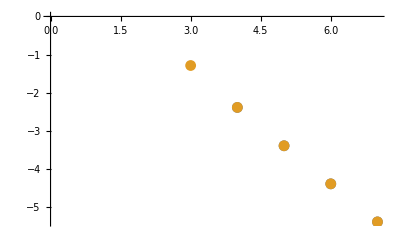

```mathematica
ListPlot[Log10@Table[{bias[1,10^n,0.5 10^n],bias3[1,10^n,0.5 10^n]},{n,0,6}]ᵀ,PlotRange->All]
```

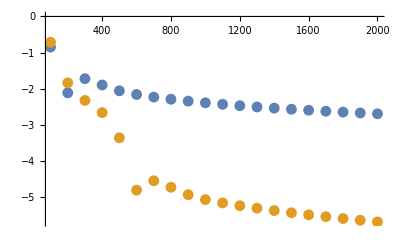

```mathematica
ListPlot[{
Table[{α,Log10@Abs[bias[1,α,0.5 α]]},{α,100,2000,100}],
Table[{α,Log10@Abs[bias[1,α,0.5 α]-bias3[1,α,0.5 α]]},{α,100,2000,100}]
},PlotRange->All]
```

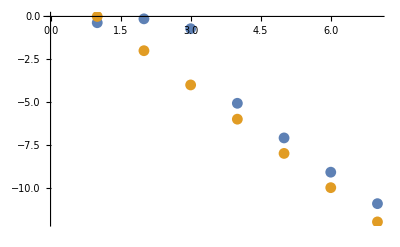

```mathematica
ListPlot[Log10@Table[{Abs[bias[1,10^n,0.5 10^n]-bias3[1,10^n,0.5 10^n]],(1/10^(2n))},{n,0,6}]ᵀ,PlotRange->All]
```

```mathematica
g[α_]:=First@NMaximize[{Exp[-α (1+Cos[ϕ])]-Exp[-α(π-ϕ)^2/2],0<ϕ<π},ϕ]
h[α_]:=NIntegrate[Exp[-α (1+Cos[ϕ])]-Exp[-α(π-ϕ)^2/2],{ϕ,0,π}]
```

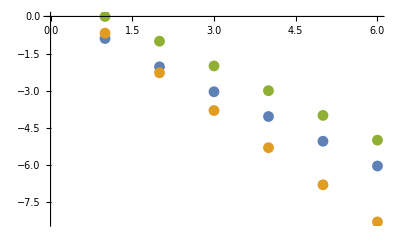

```mathematica
ListPlot[Log10@Table[{g[10^n],h[10^n],(1/10^n)},{n,0,5}]ᵀ,PlotRange->All]
```

```mathematica
Log10@Table[{g[10^n],h[10^n],(1/10^n)},{n,0,5}]ᵀ
```

{{-0.892304,-2.03579,-3.04381,-4.04459,-5.04467,-6.04468},{-0.673626,-2.27839,-3.80257,-5.30479,-6.80501,-8.30503},{0,-1,-2,-3,-4,-5}}

```mathematica
Fit[#,{1,x},x]&/@(Log10@Table[{g[10^n],h[10^n],(1/10^n)},{n,0,5}]ᵀ)
```

{0.0612909-1.02255 x,0.795673-1.52112 x,1.-1. x}

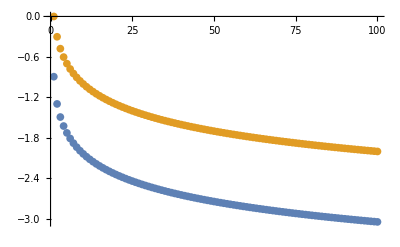

```mathematica
ListPlot[Table[{g[k],1/k},{k,1,100}]ᵀ,PlotRange->All]
```

```mathematica
FullSimplify[Sin[ϕ]^-1 Exp[-(α+β)(1+Cos[ϕ])]((γ+β Cos[ϕ])Sin[(α-β)Sin[ϕ]]+β Sin[ϕ]Cos[(α-β)Sin[ϕ]])/.{ϕ->ArcCos[t-1]},Assumptions->0<t<2]
```

(ⅇ^(-t (α+β)) (t β Cosh[√((-2+t) t) (α-β)]+(t ((-1+t) β+γ) Sinh[√((-2+t) t) (α-β)])/(√((-2+t) t))))/t

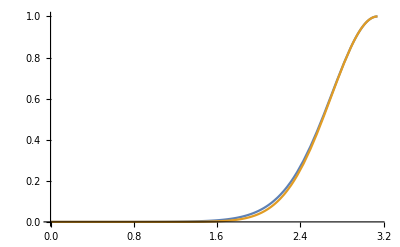

```mathematica
Plot[{Exp[-5(1+Cos[ϕ])],Exp[-5(ϕ-π)^2/2]},{ϕ,0,π}]
```

```mathematica
bias[.75,500,300]
```

0.00815996

```mathematica
Series[(t β Cosh[√((-2+t) t) (α-β)]+(t ((-1+t) β+γ) Sinh[√((-2+t) t) (α-β)])/(√((-2+t) t)))/t,{t,0,1}]//FullSimplify
```

(β^2+α γ-β (-1+α+γ))+1/3 (α-β) (β (3+α^2+β (3+β)-α (3+2 β))-(α-β)^2 γ) t+O[t]^(3/2)

```mathematica
Integrate[ⅇ^(-t (α+β))(β^2+α γ-β (-1+α+γ))+1/3 (α-β) (β (3+α^2+β (3+β)-α (3+2 β))-(α-β)^2 γ) t,{t,0,2}]//FullSimplify
```

2/3 (α-β) (β (3+α^2+β (3+β)-α (3+2 β))-(α-β)^2 γ)+((1-ⅇ^(-2 (α+β))) (β^2+α γ-β (-1+α+γ)))/(α+β)

```mathematica
2/3 (α-β) (β (3+α^2+β (3+β)-α (3+2 β))-(α-β)^2 γ)+((1-ⅇ^(-2 (α+β))) (β^2+α γ-β (-1+α+γ)))/(α+β)/.{α->500,β->300,γ->450.}
```

-8.2388×10^8

```mathematica
Series[Exp[-(α+β)(1+Cos[ϕ])]((γ+β Cos[ϕ])Sin[(α-β)Sin[ϕ]]+β Sin[ϕ]Cos[(α-β)Sin[ϕ]]),{ϕ,π,3}]
```

(-β+(-α+β) (-β+γ)) (ϕ-π)+(1/2 β (-α+β)+1/6 (β+3 α^2 β-6 α β^2+3 β^3)+((α-β)/6-1/6 (-α+β)^3) (-β+γ)+(-α/2-β/2) (-β+(-α+β) (-β+γ))) (ϕ-π)^3+O[ϕ-π]^4

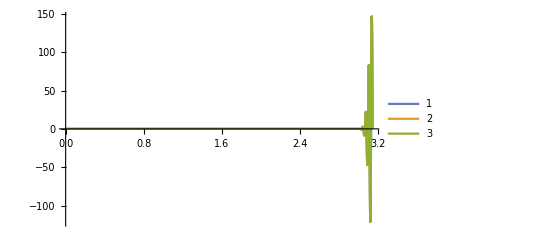

```mathematica
With[{α=500,β=300,γ=450},
Plot[{
Exp[-(α+β)(1+Cos[ϕ])]((γ+β Cos[ϕ])Sin[(α-β)Sin[ϕ]]+β Sin[ϕ]Cos[(α-β)Sin[ϕ]]),
Exp[-(α+β)1/2 (ϕ-π)^2]((γ+β Cos[ϕ])Sin[(α-β)(π-ϕ)]+β Sin[ϕ]Cos[(α-β)(π-ϕ)]),
Exp[-(α+β)1/2 (ϕ-π)^2]((γ-β )Sin[(α-β)(π-ϕ)] -(ϕ-π)β Cos[(α-β)(π-ϕ)])
},
{ϕ,0,π},
PlotRange->All,
PlotLegends->Automatic,
PlotStyle->Thick
]
]
```

```mathematica
θ=ϕ-π
dθ=dϕ
```

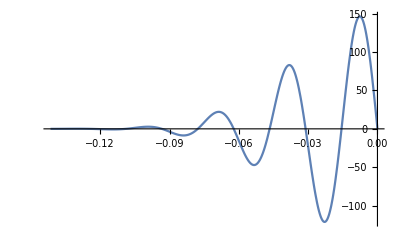

```mathematica
Plot[Exp[-(α+β)1/2 θ^2](-(γ-β )Sin[(α-β)θ] -θ β Cos[(α-β)θ])/.{ϵ->0,α->500,β->300.,γ->450},{θ,-.1415,0},PlotRange->All]
```

```mathematica
NIntegrate[Exp[-(α+β)1/2 (ϕ-π)^2]((γ-β )Sin[(α-β)(π-ϕ)] -(ϕ-π)β Cos[(α-β)(π-ϕ)])/.{α->500,β->300,γ->450},{ϕ,0,π}]-.75
NIntegrate[Exp[-(α+β)1/2 θ^2](-(γ-β )Sin[(α-β)θ] -θ β Cos[(α-β)θ])/.{α->500,β->300,γ->450},{θ,-∞,0}]-.75
```

0.00800278

0.00800278

```mathematica
bias[.75]
```

0.00815996

```mathematica
Integrate[Exp[-(α+β)1/2 θ^2](-(γ-β )Sin[(α-β)θ] -θ β Cos[(α-β)θ]),{θ,-∞,0}]//FullSimplify
```

(β √(α+β)+√2 (-2 α β+(α+β) γ) DawsonF[(α-β)/(√2 √(α+β))])/(α+β)^(3/2)

```mathematica
(p-β/(α+β)) Sqrt[2](α-β)/Sqrt[α+β] DawsonF[(α-β)/(√2 √(α+β))]-(β √(α+β)+√2 (-2 α β+(α+β) γ) DawsonF[(α-β)/(√2 √(α+β))])/(α+β)^(3/2)//FullSimplify
```

(-β √(α+β)+√2 (α+β) (p (α-β)+β-γ) DawsonF[(α-β)/(√2 √(α+β))])/(α+β)^(3/2)

```mathematica
bias[p_?NumericQ,α_,β_]:=NIntegrate[Exp[-(α+β)(1+Cos[ϕ])]((β+(α-β)p+β Cos[ϕ])Sin[(α-β)Sin[ϕ]]+β Sin[ϕ]Cos[(α-β)Sin[ϕ]]),{ϕ,3,π}]-p
```

```mathematica
bias2[p_,α_,β_]=N@1/(α+β)^(3/2)(β √(α+β)+√2 (-2 α β+(α+β) (β+(α-β)p)) DawsonF[(α-β)/(√2 √(α+β))])-p;
bias3[p_,α_,β_]=N@(p-β/(α+β)) (Sqrt[2](α-β)/Sqrt[α+β] DawsonF[(α-β)/(√2 √(α+β))]-1);
```

```mathematica
Limit[Series[Sqrt[2]x DawsonF[x/Sqrt[2]],{x,n,2}],n->∞]
```

1

```mathematica
Sqrt[2]x((1/(2x)+1/(4 x^3)+3/(8 x^5))/.x->x/Sqrt[2])//Simplify
```

1+3/x^4+1/x^2

```mathematica
Series[1+Cos[ϕ],{ϕ,π,4}]
```

1/2 (ϕ-π)^2-1/24 (ϕ-π)^4+O[ϕ-π]^5

```mathematica
Integrate[-2 γ Exp[-α-β+2Sqrt[α β]]Exp[-Sqrt[α β] t^2]/t,{t,I(Sqrt@Sqrt[α/β]+Sqrt@Sqrt[β/α]),∞}]
```

ⅇ^(-α-β+2 √(α β)) γ (ⅈ π+ExpIntegralEi[α+β+2 √(α β)])

```mathematica
Integrate[-Exp[-α-β]Exp[-Sqrt[α β]t]Sqrt[α β]/t,{t,-(Sqrt[α/β]+Sqrt[β/α]),I(Sqrt[α/β]+Sqrt[β/α]),(Sqrt[α/β]+Sqrt[β/α]),∞}]
```

ⅇ^(-α-β) √(α β) (ⅈ π-ExpIntegralEi[-α-β]+ExpIntegralEi[-ⅈ (α+β)])+ⅇ^(-α-β) √(α β) (-ExpIntegralEi[-ⅈ (α+β)]+ExpIntegralEi[α+β])-ⅇ^(-α-β) √(α β) Gamma[0,α+β]

```mathematica
ⅇ^(-α-β) √(α β) (ⅈ π-ExpIntegralEi[-α-β]+ExpIntegralEi[-ⅈ (α+β)])+ⅇ^(-α-β) √(α β) (-ExpIntegralEi[-ⅈ (α+β)]+ExpIntegralEi[α+β])-ⅇ^(-α-β) √(α β) Gamma[0,α+β]//FullSimplify
```

ⅇ^(-α-β) √(α β) (ⅈ π+ExpIntegralEi[α+β])

```mathematica
ⅇ^(-α-β) √(α β) (ⅈ π+ExpIntegralEi[α+β])+ⅇ^(-α-β+2 √(α β)) γ (ⅈ π+ExpIntegralEi[α+β+2 √(α β)])//FunctionExpand
```

ⅇ^(-α-β) √(α β) (ⅈ π+ExpIntegralEi[α+β])+ⅇ^(-α-β+2 √(α β)) γ (ⅈ π+ExpIntegralEi[α+β+2 √(α β)])

```mathematica
ExpIntegralEi[600.]
```

6.29888×10^257

```mathematica
ⅇ^(-α-β) (√(α β) (ⅈ π+ExpIntegralEi[α+β])+ⅇ^(2 √(α β)) γ (ⅈ π+ExpIntegralEi[α+β+2 √(α β)]))/.{α->5.,β->3,γ->4.5}
```

1.64058×10^6+10.9698 ⅈ

```mathematica
bias[300/800,500,300]
bias2[300/800,500,300]
bias3[300/800,500,300]
```

0.0000762926

0.

0.

```mathematica
p/.First@Solve[1/(α+β)^(3/2)(β √(α+β)+√2 (-2 α β+(α+β) (β+(α-β)p)) DawsonF[(α-β)/(√2 √(α+β))])-p==0,p]//FullSimplify
```

β/(α+β)

```mathematica
D[1/(α+β)^(3/2)(β √(α+β)+√2 (-2 α β+(α+β) (β+(α-β)p)) DawsonF[(α-β)/(√2 √(α+β))])-p,p]//FullSimplify
```

-1+(√2 (α-β) DawsonF[(α-β)/(√2 √(α+β))])/(√(α+β))

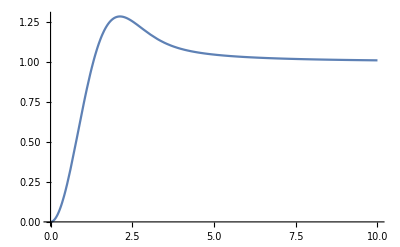

```mathematica
Plot[Sqrt[2]x DawsonF[x/Sqrt[2]],{x,0,10},PlotRange->All]
```

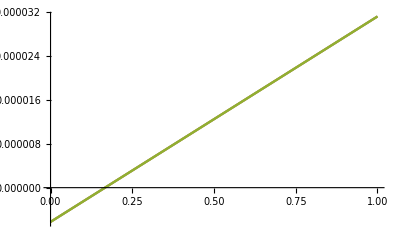

```mathematica
With[{α=50000,β=10000},
Plot[{bias[p,α,β],Re@bias2[p,α,β],bias3[p,α,β]},{p,0,1}]
]
```

```mathematica
1/60000.
```

0.0000166667

```mathematica
Series[Log[Exp[-(α+β)(1+Cos[ϕ])]((γ+β Cos[ϕ])Sin[(α-β)Sin[ϕ]]+β Sin[ϕ]Cos[(α-β)Sin[ϕ]])],{ϕ,π,3}]//Normal//FullSimplify
```

-(((β^4+α (1+α (3+α)) γ-β^3 (-6+3 α+γ)-β (-1+α+α^3+γ+3 α^2 γ)+β^2 (7-3 γ+3 α (-2+α+γ))) (π-ϕ)^2)/(6 (β^2+α γ-β (-1+α+γ))))+Log[-β+(α-β) (β-γ)]+Log[-π+ϕ]

```mathematica
formula=Integrate[Exp[-(α+β)(1+Cos[ϕ])]((β+(α-β)p+β Cos[ϕ])Sin[(α-β)Sin[ϕ]]+β Sin[ϕ]Cos[(α-β)Sin[ϕ]]),{ϕ,0,π}]
```

∫_0^π ⅇ^((-α-β) (1+Cos[ϕ])) (β Cos[(α-β) Sin[ϕ]] Sin[ϕ]+(γ+β Cos[ϕ]) Sin[(α-β) Sin[ϕ]])ⅆϕ

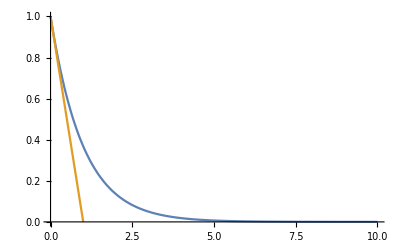

```mathematica
Plot[{Exp[-x],1-x},{x,0,10},PlotRange->{0,1}]
```

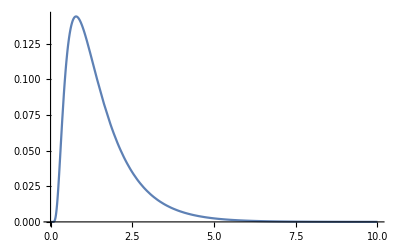

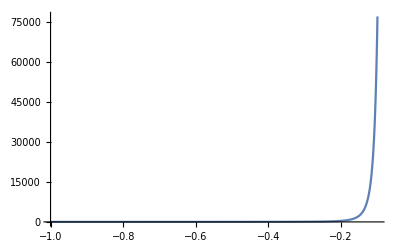

```mathematica
Plot[Exp[-x-1/x]/Sqrt[x],{x,0,10}]
Plot[I Exp[-x-1/x]/Sqrt[x],{x,-1,-.1},PlotRange->All]
```

```mathematica
Residue[ⅈ ⅇ^(-α-t α-((1+t) β)/t) √t γ+(ⅈ ⅇ^(-α-t α-((1+t) β)/t) β)/(√t),{t,0}]
```

Residue[(ⅈ ⅇ^(-α-t α-((1+t) β)/t) β)/(√t)+ⅈ ⅇ^(-α-t α-((1+t) β)/t) √t γ,{t,0}]

Therefore the quantity of interest is given by the following, which needs complex analysis to compute because of the pole at t=0.

```mathematica
Integrate[ⅈ ⅇ^(-α-t α-((1+t) β)/t) √t γ+(ⅈ ⅇ^(-α-t α-((1+t) β)/t) β)/(√t),{t,-1,∞}]
```

```mathematica
I Exp[-α-β]Integrate[Exp[-α t-β/t](γ Sqrt[t]+β/Sqrt[t]),{t,0,∞}]//FullSimplify
```

(ⅈ ⅇ^(-α-β-2 √(α β)) √π (2 α β+γ+2 √(α β) γ))/(2 α^(3/2))

```mathematica
NIntegrate[( Exp[-α-β]Exp[-α Exp[I ϕ]-β Exp[-I ϕ]]Im@(γ Exp[I ϕ/2]+β Exp[-I ϕ/2]))/.{α->5000,β->3000.,γ->4500},{ϕ,-π,0}]
```

1.80404×10^-13-0.751509 ⅈ

```mathematica
Integrate[Exp[-α Exp[I ϕ]-β Exp[-I ϕ]](γ Exp[I ϕ/2]+β Exp[-I ϕ/2]),ϕ]
```

∫ⅇ^(-ⅇ^(ⅈ ϕ) α-ⅇ^(-ⅈ ϕ) β) (ⅇ^(-(ⅈ ϕ)/2) β+ⅇ^((ⅈ ϕ)/2) γ)ⅆϕ

```mathematica
Module[{α=5000,β=3000,p=.75,n=10000000,x,y,z},
x=N@RandomVariate[PoissonDistribution[α],n];
y=RandomVariate[PoissonDistribution[β],n];
z=RandomVariate[PoissonDistribution[p α+(1-p)β],n];
(z-y)/(x-y+1/2)
]//Mean
```

0.750561

```mathematica
NIntegrate[I(ⅈ ⅇ^(-α-t α-((1+t) β)/t)Sqrt[t] γ+(ⅈ ⅇ^(-α-t α-((1+t) β)/t) β)/Sqrt[t])/.{α->500,β->300.,γ->500,t->(I+1)ϕ-1},{ϕ,0,1}]+NIntegrate[I(ⅈ ⅇ^(-α-t α-((1+t) β)/t)Sqrt[t] γ+(ⅈ ⅇ^(-α-t α-((1+t) β)/t) β)/Sqrt[t])/.{α->500,β->300.,γ->500,t->(1-I)ϕ+I},{ϕ,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

-0.502728-0.502728 ⅈ

```mathematica
|
```

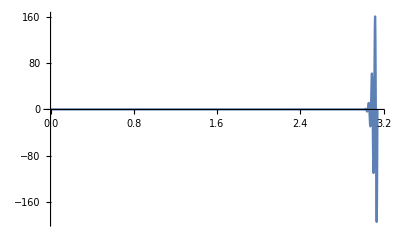

```mathematica
Plot[-Re[(ⅇ^(-ⅇ^(-ⅈ ϕ) (1+ⅇ^(ⅈ ϕ)) (ⅇ^(ⅈ ϕ) α+β)) (β+ⅇ^(ⅈ ϕ) γ))/(√(ⅇ^(ⅈ ϕ)))]/.{α->500,β->300.,γ->500},{ϕ,0,π},PlotRange->All]
```

```mathematica
Plot3D[Re[Exp[-α(1+ t)-β(1+1/t)](γ+β t)/.{α->500,β->300.,γ->450,t->x+I y}],{x,-1,-.8},{y,-.1,.1},PlotRange->All]
Plot3D[Im[Exp[-α(1+ t)-β(1+1/t)](γ+β t)/.{α->500,β->300.,γ->450,t->x+I y}],{x,-1,-.8},{y,-.1,.1},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

### Bias Corrected Estimator

```mathematica
(z-y)/(x-y)-((z-y)/(x-y)-y/(x-y))(x+y)/(x-y)^2//FullSimplify
```

(-y (x^2+(-2+y) y-2 x (1+y))+(x^2+(-1+y) y-x (1+2 y)) z)/(x-y)^3

```mathematica
(-y (x^2+(-2+y) y-2 x (1+y))+(x^2+(-1+y) y-x (1+2 y)) z)/(x-y)^3/.{x->5000,y->3000,z->4500.}
```

0.7515

```mathematica
Module[{α=500,β=300,p=1,n=1000000,x,y,z},
x=N@RandomVariate[PoissonDistribution[α],n];
y=RandomVariate[PoissonDistribution[β],n];
z=RandomVariate[PoissonDistribution[p α+(1-p)β],n];
{
Mean[(z-y)/(x-y+.2)],
Mean[(-y (x^2+(-2+y) y-2 x (1+y))+(x^2+(-1+y) y-x (1+2 y)) z)/(x-y)^3]
}
]
```

{1.01237,1.02604}

```mathematica
x^2+(-2+y) y-2 x (1+y)//Expand
```

-2 x+x^2-2 y-2 x y+y^2